-----------------------------------Euler with simple FOR loop------------------------------------

```mathematica
f1[x_,y_]=-2 x^3+12 x^2-20x+8.5;
yi=1.0;
xi=0;
xf=4;  
nmax=20;
h=(xf-xi)/nmax//N;
datalist={};
yprev=yi;
xprev=xi;
datalist=Append[datalist,{xprev,yprev}];
For[n=1,
      n<=nmax,
      n++,
      xnext=xprev+h;
      ynext=yprev+ h  f1[xprev,yprev];
     datalist=Append[datalist,{xnext,ynext}];
     yprev=ynext;
     xprev=xnext;
]
```

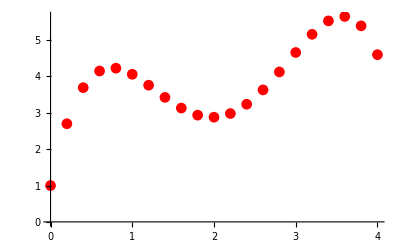

```mathematica
dataploteuler=ListPlot[datalist,PlotStyle->Red,PlotMarkers->Automatic]
```

-----------------RK4 with simple FOR loop---------------------------------

```mathematica
datalist2={};
yprev=yi;
xprev=xi;
datalist2=Append[datalist2,{xprev,yprev}]
```

{{0,1.}}

```mathematica
For[n=1,
      n<=nmax,
      n++,
      xnext=xprev+h;
      k1=f1[xprev,yprev];
      k2 = f1[xprev+1/2 h,yprev+1/2 k1 h];
       k3 = f1[xprev+1/2 h,yprev+1/2 k2 h];
       k4 = f1[xprev+ h,yprev+ k3 h];
      ynext=yprev+ 1/6(k1+2k2+2k3+k4)h;
     datalist2=Append[datalist2,{xnext,ynext}];
     yprev=ynext;
     xprev=xnext;
]
```

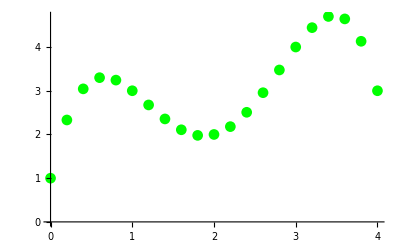

```mathematica
dataplotrk4=ListPlot[{datalist2},PlotStyle->Green,PlotMarkers->Automatic]
```

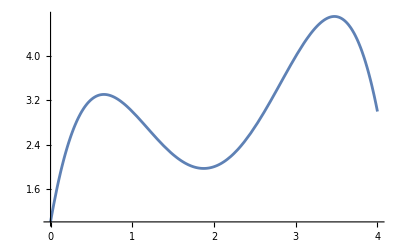

```mathematica
solutionplot=Plot[-0.5 x^4+4 x^3-10 x^2+8.5 x +1,{x,xi,xf}]
```

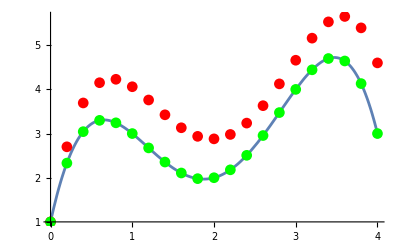

```mathematica
Show[solutionplot,dataploteuler,dataplotrk4,PlotRange->Full]
```

```mathematica
datalist2[[All,2]]
```

{1.,2.3312,3.0432,3.2992,3.2432,3.,2.6752,2.3552,2.1072,1.9792,2.,2.1792,2.5072,2.9552,3.4752,4.,4.4432,4.6992,4.6432,4.1312,3.}

```mathematica
datalist[[All,2]]
```

{1.,2.7,3.6928,4.1512,4.2288,4.06,3.76,3.4248,3.1312,2.9368,2.88,2.98,3.2368,3.6312,4.1248,4.66,5.16,5.5288,5.6512,5.3928,4.6}

```mathematica
diff=datalist[[All,2]]-datalist2[[All,2]]
```

{0.,0.3688,0.6496,0.852,0.9856,1.06,1.0848,1.0696,1.024,0.9576,0.88,0.8008,0.7296,0.676,0.6496,0.66,0.7168,0.8296,1.008,1.2616,1.6}

```mathematica
Mean[diff]
```

0.850667

## Damped anharmonic oscillator

x^(..) + dẋ - ax + bx^3 = 0